```mathematica
A = {{2,1},{1,2}};
es = Eigensystem[A];
Λ = DiagonalMatrix[es[[1]]];
R = es[[2]];
Λ//MatrixForm
R//MatrixForm
Inverse[R].Λ.R-A//MatrixForm
```

(3 | 0
0 | 1)

(1 | 1
-1 | 1)

(0 | 0
0 | 0)

```mathematica
q0[x_]:={{ⅇ^(-x^2)},{ⅇ^(-(x-2)^2)}}
w0[x_]:=R.q0[x]
w[x_,t_]:={{w0[x][[1]]},{w0[x][[2]]}}
```

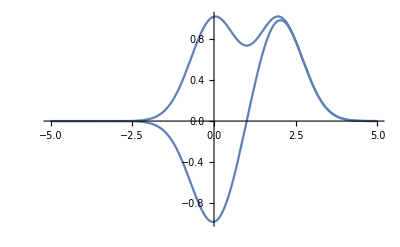

```mathematica
Plot[w[x,0],{x,-5,5}]
```

```mathematica
w[x,t]
```

{{{ⅇ^(-(-2+x)^2)+ⅇ^(-x^2)}},{{ⅇ^(-(-2+x)^2)-ⅇ^(-x^2)}}}

```mathematica
w0[x]
```

{{ⅇ^(-(-2+x)^2)+ⅇ^(-x^2)},{ⅇ^(-(-2+x)^2)-ⅇ^(-x^2)}}